## FitEllipse-example.nb FitEllipse, PrimaryAxes

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51a (07 June 2017)) loaded Thu 8 Jun 2017 13:39:36
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

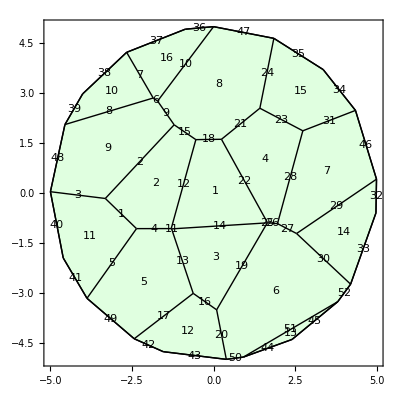

```mathematica
w=TemplateRandomCircularGrid[16,5];
ShowTissue[w, "CellNumbers"-> True, "EdgeNumbers"-> True, Frame-> True]
```

```mathematica
v6=CellVertexCoordinates[w,6]
```

{{3.79573,-3.25461},{4.18928,-2.72946},{2.53525,-1.20886},{1.95095,-0.912507},{1.64544,-0.885419},{1.63924,-0.888614},{0.088453,-3.49854},{0.38472,-4.98518},{0.908247,-4.91682}}

```mathematica
FitEllipse[v6]
```

{Angle→1.08189,Axes→{2.08084,1.41727},Graphics→-Graphics-}

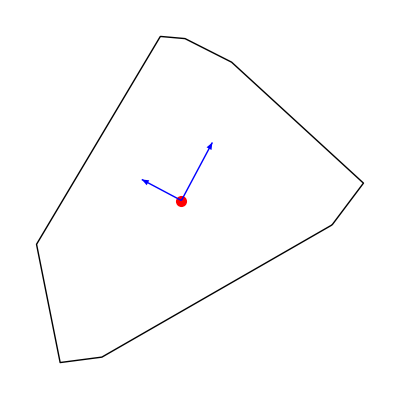
{Vectors→{{{1.9055,-2.94812},{2.29367,-2.21845}},{{1.9055,-2.94812},{1.40851,-2.68374}}},Graphics→-Graphics-,Eigenvalues→{0.826502,0.562933},Angles→{1.08189,2.65269}}

```mathematica
PrimaryAxes[v6]
```

```mathematica
v=CellVertexCoordinates[w];
```

```mathematica
Show[("Graphics"/.FitEllipse[#])&/@v]
```

-Graphics-